```mathematica
(* Model parameters using um and second units *)
k0f=1*10^5
k0r=139
k1f=0.32
k1r=1.2*10^2
k2f=4.3*10^-4
k2r=1.0*10^-10
k3=1.4*10^-3
```

100000

139

0.32

120.

0.00043

1.×10^-10

0.0014

```mathematica
kk=k0r*k1f/((k0r+k0f)*k1r)
```

3.70152×10^-6

```mathematica
k3/k2f
```

3.25581

```mathematica
(* differential equations *)
eqt2nsb=t2nsb'[t]==k0f*t2[t]-k0r*t2nsb[t]
eqt2=t2'[t]==-k0f*t2[t]+k0r*t2nsb[t]-k1f*t2[t]*(2*ab[t]+t2ab[t]+abt2[t])+k1r*(t2ab[t]+abt2[t]+2*t2abt2[t])+k3*at2b[t]
eqab=ab'[t]==-2*k1f*t2[t]*ab[t]+k1r*t2ab[t]+k1r*abt2[t]+k3*at2b[t]
eqt2ab=t2ab'[t]==k1f*ab[t]*t2[t]-k1r*t2ab[t]-k1f*t2ab[t]*t2[t]+k1r*t2abt2[t]-k2f*t2ab[t]+k2r*at2b[t]
eqabt2=abt2'[t]==k1f*ab[t]*t2[t]-k1r*abt2[t]-k1f*abt2[t]*t2[t]+k1r*t2abt2[t]-k2f*abt2[t]+k2r*at2b[t]
eqt2abt2=t2abt2'[t]==k1f*t2ab[t]*t2[t]+k1f*abt2[t]*t2[t]-2*k1r*t2abt2[t]
eqat2b=at2b'[t]==k2f*t2ab[t]+k2f*abt2[t]-2*k2r*at2b[t]-k3*at2b[t]
eqx=x'[t]==k3*at2b[t]
```

t2nsb'[t]==100000 t2[t]-139 t2nsb[t]

t2'[t]==0.0014 at2b[t]-100000 t2[t]-0.32 t2[t] (2 ab[t]+abt2[t]+t2ab[t])+120. (abt2[t]+t2ab[t]+2 t2abt2[t])+139 t2nsb[t]

ab'[t]==120. abt2[t]+0.0014 at2b[t]-0.64 ab[t] t2[t]+120. t2ab[t]

t2ab'[t]==1.×10^-10 at2b[t]+0.32 ab[t] t2[t]-120. t2ab[t]-0.32 t2[t] t2ab[t]+120. t2abt2[t]

abt2'[t]==-120. abt2[t]+1.×10^-10 at2b[t]+0.32 ab[t] t2[t]-0.32 abt2[t] t2[t]+120. t2abt2[t]

t2abt2'[t]==0.32 abt2[t] t2[t]+0.32 t2[t] t2ab[t]-240. t2abt2[t]

at2b'[t]==0.00043 abt2[t]-0.0014 at2b[t]+0.00043 t2ab[t]

x'[t]==0.0014 at2b[t]

```mathematica
(* 10^6 seconds is about 11 days *)
maxtime=1*10^6
```

1000000

```mathematica
soln=NDSolve[{eqt2nsb,eqt2,eqab,eqt2ab,eqabt2,eqt2abt2,eqat2b,eqx,
t2nsb[0]==1.0*10^6,t2[0]==0,ab[0]==1/500,t2ab[0]==0,abt2[0]==0,t2abt2[0]==0,at2b[0]==0,x[0]==0},
{t2nsb,t2,ab,t2ab,abt2,t2abt2,at2b,x},
{t,0,maxtime}];
```

```mathematica
{t2nsbeq,t2eq,abeq,t2abeq,abt2eq,t2abt2eq,at2beq,xmax}=Evaluate[{t2nsb[t],t2[t],ab[t],t2ab[t],abt2[t],t2abt2[t],at2b[t],x[t]}/.Flatten[{soln,t->maxtime}]]
```

{998612.,1388.07,0.0000820411,0.000303676,0.000303676,0.00112406,0.000186544,0.260992}

```mathematica
(* check some equations in the analytical theory *)
{t2toteq=t2nsbeq+t2eq,10^6}
{abtoteq=abeq+t2abeq+abt2eq+t2abt2eq,N[1/500]}
{t2nsbeq/t2eq,N[k0f/k0r]}
{t2eq/t2toteq,N[k0r/(k0f+k0r)]}
{t2abeq/(t2eq*abeq),abt2eq/(t2eq*abeq),t2abt2eq/(t2eq*t2abeq),t2abt2eq/(t2eq*abt2eq),N[k1f/k1r]}
{t2abeq/abtoteq,abt2eq/abtoteq,kk*t2toteq/(1+2*kk*t2toteq+kk^2*t2toteq^2)}
{k2f*(t2abeq+abt2eq),xmax/maxtime}
```

{1.×10^6,1000000}

{0.00181346,0.002}

{719.424,719.424}

{0.00138807,0.00138807}

{0.00266666,0.00266666,0.00266667,0.00266667,0.00266667}

{0.167457,0.167457,0.167457}

{2.61161×10^-7,2.60992×10^-7}

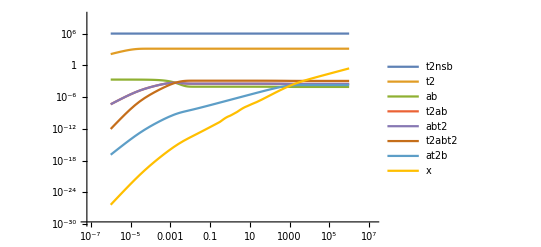

```mathematica
(* The following figure shows several characteristic times,
t2nsb and t2 equilibrate at about 10^-5 s;
ab, t2ab (same as abt2), abt2, and t2abt2 equilibrate at about 10^-3 s;
at2b equilibrates at about 10^3 s. *)
LogLogPlot[Evaluate[{t2nsb[t],t2[t],ab[t],t2ab[t],abt2[t],t2abt2[t],at2b[t],x[t]}/.soln],
{t,0.000001,1000000},
PlotLegends->{"t2nsb","t2","ab","t2ab","abt2","t2abt2","at2b","x"},
PlotRange->Automatic]
```

```mathematica
solution[t2tot_]:=NDSolve[{eqt2nsb,eqt2,eqab,eqt2ab,eqabt2,eqt2abt2,eqat2b,eqx,
t2nsb[0]==t2tot,t2[0]==0,ab[0]==1/500,t2ab[0]==0,abt2[0]==0,t2abt2[0]==0,at2b[0]==0,x[0]==0},
{t2nsb,t2,ab,t2ab,abt2,t2abt2,at2b,x},
{t,0,maxtime}];
```

```mathematica
s10=N[Sqrt[10]]
```

3.16228

```mathematica
xaxis={10^2,s10*10^2,10^3,s10*10^3,10^4,s10*10^4,10^5,s10*10^5,10^6,s10*10^6,10^7,s10*10^7,10^8,s10*10^8,10^9}
```

{100,316.228,1000,3162.28,10000,31622.8,100000,316228.,1000000,3.16228×10^6,10000000,3.16228×10^7,100000000,3.16228×10^8,1000000000}

```mathematica
simdata=Table[(
Evaluate[x[t]/.Flatten[{solution[t2tot],t->maxtime}]]-
Evaluate[x[t]/.Flatten[{solution[t2tot],t->maxtime/2}]])/(maxtime/2),{t2tot,xaxis}]
```

{6.36044×10^-10,2.00715×10^-9,6.30549×10^-9,1.95325×10^-8,5.79763×10^-8,1.52556×10^-7,3.02495×10^-7,3.70759×10^-7,2.61161×10^-7,1.19403×10^-7,4.33724×10^-8,1.43722×10^-8,4.61412×10^-9,1.46615×10^-9,4.64346×10^-10}

```mathematica
plotdata=Transpose[{xaxis,simdata}]
```

{{100,6.36044×10^-10},{316.228,2.00715×10^-9},{1000,6.30549×10^-9},{3162.28,1.95325×10^-8},{10000,5.79763×10^-8},{31622.8,1.52556×10^-7},{100000,3.02495×10^-7},{316228.,3.70759×10^-7},{1000000,2.61161×10^-7},{3.16228×10^6,1.19403×10^-7},{10000000,4.33724×10^-8},{3.16228×10^7,1.43722×10^-8},{100000000,4.61412×10^-9},{3.16228×10^8,1.46615×10^-9},{1000000000,4.64346×10^-10}}

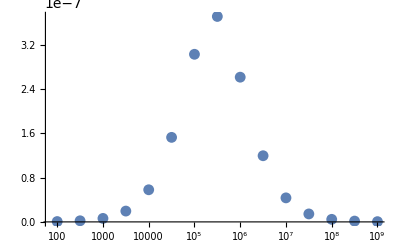

```mathematica
ListLogLinearPlot[plotdata]
```

```mathematica
phi[t2tot_,abtot_]=2*k2f*kk*t2tot*abtot/(1+2*kk*t2tot+kk^2*t2tot^2)
```

(3.18331×10^-9 abtot t2tot)/(1+7.40304×10^-6 t2tot+1.37013×10^-11 t2tot^2)

```mathematica
phi2[t2tot_,abtot_]=2*k2f*kk*t2tot*abtot/(1+2*kk*t2tot+kk^2*t2tot^2)*(2*k2f*kk*t2tot/((2*k2r+k3)*(1+2*kk*t2tot+kk^2*t2tot^2))+1)^-1
```

(3.18331×10^-9 abtot t2tot)/((1+7.40304×10^-6 t2tot+1.37013×10^-11 t2tot^2) (1+(2.27379×10^-6 t2tot)/(1+7.40304×10^-6 t2tot+1.37013×10^-11 t2tot^2)))

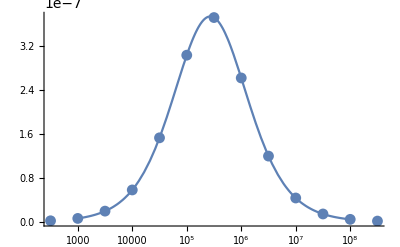

```mathematica
Show[{LogLinearPlot[phi2[t2tot,1/500],{t2tot,1000,100000000}],
ListLogLinearPlot[plotdata]}]
```

```mathematica
(* 1 molecule per cubic micron = 0.00166 uM *)
um2uM=1000000^3/1000/(6.022*10^23)*1000000
```

0.00166058

```mathematica
(* 1 year = 3.2e7 seconds *)
sec2year=60*60*24*365.24
```

3.15567×10^7

```mathematica
plotdata2=Transpose[{xaxis*um2uM,simdata*sec2year}]
```

{{0.166058,0.0200715},{0.525121,0.0633391},{1.66058,0.198981},{5.25121,0.616383},{16.6058,1.82954},{52.5121,4.81417},{166.058,9.54576},{525.121,11.6999},{1660.58,8.2414},{5251.21,3.76798},{16605.8,1.36869},{52512.1,0.453541},{166058.,0.145606},{525121.,0.046267},{1.66058×10^6,0.0146532}}

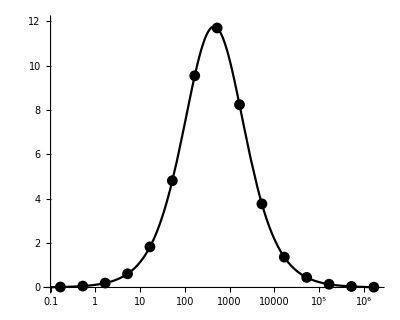

```mathematica
Show[{LogLinearPlot[phi2[t2tot/um2uM,1/500]*sec2year,{t2tot,0.1,2000000},PlotStyle->Black],
ListLogLinearPlot[plotdata2,PlotStyle->Black]},
AspectRatio->0.8,PlotRange->{{Log[0.1],Log[2000000]},{0,12}},AxesOrigin->{Log[0.1],0},TicksStyle->{Thick,Thick},AxesStyle->Bold]
```